```mathematica
m=4*938.272046(*Mega ElectronVolt*);
ℏc=197.32697178(*Mega ElectronVolt*Femto Meter*);
R=2 (*Femto Meter*);
V0=-41.6(*Mega ElectronVolt*);
a=.2(*Femto Meter*);
V[r_]:=V0/(1+E^((r-R)/a));
(*k=4*)
```

```mathematica
s[L_,k_]:=NDSolve[{u''[r]+(k^2-2*m/(ℏc)^2*V[r]-L*(L+1)/r^2)*u[r]==0,u[(1000*k)^(-1)]==0,u'[(1000*k)^(-1)]==8},u,{r,(1000*k)^(-1),5*R},MaxSteps->20000]
```

```mathematica
u[L_,k_,r_]:=u[r]/.s[L,k][[1]]
```

```mathematica
β[L_,k_]:=5*R/Evaluate[u[L,k,5*R]]*(D[u[L,k,r],r]/.r->(5*R))-1
tanδ[L_,k_]:=N[(k*5*R*Derivative[0,1][SphericalBesselJ][L,k*5*R]-β[L,k]*SphericalBesselJ[L,k*5*R])/(k*5*R*Derivative[0,1][SphericalBesselY][L,k*5*R]-β[L,k]*SphericalBesselY[L,k*5*R])]
```

```mathematica
f[k_,θ_]:=1/k*Sum[(2*L+1)*tanδ[L,k]/(1-I*tanδ[L,k])*LegendreP[L,Cos[θ]],{L,0,2*k*R}]
```

```mathematica
dσdΩ[k_,points_:10]:=Table[{θ,Abs[f[k,θ]]^2},{θ,0,Pi,N[1/points]}]
```

```mathematica
χ0[k_,b_]=-2*m/(k*(ℏc)^2)*NIntegrate[V[Sqrt[b^2+z^2]],{z,0,15}];
T0[k_,b_]:=Exp[I*χ0[k,b]]-1
Eif0[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*T0[k,b],{b,0,15}]
```

```mathematica
eik0dσdΩ[k_,points_:10]:=Table[{N[θ/points],Abs[Eif0[k,θ/points]]^2},{θ,0,points*Pi,1}]
```

```mathematica
En[k_]:=(k*ℏc)^2/(2*m)
U[r_]:=V[r]/V0
ϵ[k_]:=V0/(2*En[k])
```

```mathematica
τ1[k_,b_]=-k*ϵ[k]^2*NIntegrate[Evaluate[(1#+b*D[#,b])&[U[Sqrt[z^2+b^2]]^2]],{z,0,15}];
```

```mathematica
T1[k_,b_]:=Exp[I(χ0[k,b]+τ1[k,b])]-1
Eif1[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*T1[k,b],{b,0,15}]
```

```mathematica
eik1dσdΩ[k_,points_:10]:=Table[{N[θ/points],Abs[Eif1[k,θ/points]]^2},{θ,0,points*Pi,1}]
```

```mathematica
τ2[k_,b_]=-k*ϵ[k]^3*NIntegrate[Evaluate[(1#+5/3*b*D[#,b]+1/3*b^2*D[#,{b,2}])&[U[Sqrt[z^2+b^2]]^3]],{z,0,15}]-b*D[χ0[k,b],b]^3/(24*k^2);
ω2[k_,b_]=D[χ0[k,b],b]*D[b*D[χ0[k,b],b],b]/(8*k^2);
```

```mathematica
T2[k_,b_]:=Exp[I(χ0[k,b]+τ1[k,b]+τ2[k,b])]*Exp[-ω2[k,b]]-1
Eif2[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*T2[k,b],{b,0,15}]
```

```mathematica
eik2dσdΩ[k_,points_:10]:=Table[{N[θ/points],Abs[Eif2[k,θ/points]]^2},{θ,0,points*Pi,1}]
```

```mathematica
τ3[k_,b_]=-k*ϵ[k]^4*NIntegrate[Evaluate[(5/4#+11/4*b*D[#,b]+b^2*D[#,{b,2}]+1/12*b^3*D[#,{b,3}])&[U[Sqrt[z^2+b^2]]^4]],{z,0,15}]-b*D[τ1[k,b],b]*D[χ0[k,b],b]^2/(8*k^2);
ϕ3[k_,b_]=-k*ϵ[k]^2*NIntegrate[Evaluate[(1#+5/3*b*D[#,b]+1/3*b^2*D[#,{b,2}])&[(1/(2*k)*D[U[Sqrt[z^2+b^2]],b])^2]],{z,0,15}];
ω3[k_,b_]=(D[χ0[k,b],b]*D[b*D[τ1[k,b],b],b]+D[τ1[k,b],b]*D[b*D[χ0[k,b],b],b])/(8*k^2);
```

```mathematica
T3[k_,b_]:=Exp[I*(χ0[k,b]+τ1[k,b]+τ2[k,b]+τ3[k,b]+ϕ3[k,b])]*Exp[-(ω2[k,b]+ω3[k,b])]-1
```

```mathematica
Eif3[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*T3[k,b],{b,0,15}]
```

```mathematica
eik3dσdΩ[k_,points_:10]:=Table[{N[θ/points],Abs[Eif3[k,θ/points]]^2},{θ,0,points*Pi,1}]
```

```mathematica
dσdΩ[4]//Timing
```

```mathematica
{31.806164999999993,{{0.,268.4499238093087},{0.1,222.25077358139697},{0.2,123.64824029962246},{0.30000000000000004,43.789816734523804},{0.4,10.955670189338099},{0.5,5.985529663793322},{0.6000000000000001,5.317922669137314},{0.7000000000000001,2.855172364934782},{0.8,1.0724967920158974},{0.9,0.7100080784945664},{1.,0.6481642160137192},{1.1,0.4003670844173451},{1.2000000000000002,0.1914704459271666},{1.3,0.1377434481759826},{1.4000000000000001,0.13207850147901729},{1.5,0.09800819342470164},{1.6,0.056798315232668706},{1.7000000000000002,0.03957749100125823},{1.8,0.03961285885692868},{1.9000000000000001,0.0361652396962103},{2.,0.02523298034874482},{2.1,0.017348879735921287},{2.2,0.016768069814706882},{2.3000000000000003,0.016461254046558137},{2.4000000000000004,0.012501646002947604},{2.5,0.010274346830522339},{2.6,0.012030113960493631},{2.7,0.010604936153856728},{2.8000000000000003,0.0038758578671768337},{2.9000000000000004,0.003608594400601719},{3.,0.01785137797347571},{3.1,0.03360732478489995}}}
```

```mathematica
interp4=Interpolation[%[[2]]]
```

```mathematica
eik0dσdΩ[4]//Timing
```

```mathematica
{29.625494999999972,{{0.,194.96169649563822},{0.1,163.78116634853328},{0.2,96.27524460705108},{0.3,39.35408434524921},{0.4,13.163581998859392},{0.5,6.939466463951308},{0.6,5.393012625347566},{0.7,3.343935478232733},{0.8,1.6309961888670816},{0.9,0.8835197199557864},{1.,0.6268496598892831},{1.1,0.43585823043141236},{1.2,0.26124609258815373},{1.3,0.15262703612455258},{1.4,0.1027129042879846},{1.5,0.07675381682165934},{1.6,0.05585824489215554},{1.7,0.03820575940973819},{1.8,0.02583554100745011},{1.9,0.018494292697696736},{2.,0.01430296766293799},{2.1,0.011579208916466214},{2.2,0.00947048764062207},{2.3,0.0077210686159694545},{2.4,0.006302600842552269},{2.5,0.005209586610789415},{2.6,0.004405970746222057},{2.7,0.0038360231646486108},{2.8,0.0034441647586362354},{2.9,0.0031860030764785333},{3.,0.003030919097528283},{3.1,0.0029606208859675564}}}
```

```mathematica
eik0interp4=Interpolation[%[[2]]]
```

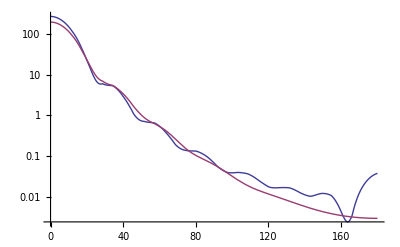

```mathematica
LogPlot[{interp4[θ*Pi/180],eik0interp4[θ*Pi/180]},{θ,0,180}]
```